This is a program written to find out what exactly happened when new perturbations of matter profiles are added.

# Prepare

```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

```mathematica
Get["../../neuPackage/neutrino.wl"]
```

```mathematica
Get["../../neuPackage/neumat.wl"]
```

# New Combinations of n’s

## Parameters

```mathematica
gF=1.17*10^(-11)(*MeV^(-2)*)
ye=0.5
```

1.17×10^-11

0.5

```mathematica
deltamsquare13=2.6*10^(-15);(*MeV^2*)
energy10=10;(*Energy in units of MeV*)
omegaV=deltamsquare13/(2 energy10)(*MeV*);(*For 10 MeV neutrinos*)
thetaV=ArcSin[√0.093/2]
```

0.153077

```mathematica
fraction=10
lambdaN=fraction*Cos[2thetaV]omegaV
```

10

1.23955×10^-15

```mathematica
Cos[2thetaV]-(lambdaN/omegaV)^2
```

-89.9627

```mathematica
thetamV=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2,Pi];
init={psi1[0],psi2[0]}=={1,0};
endpointN=1600;
```

List of Parameters for 1 2 3 frequiencies

```mathematica
onekList={0.999};
twokList={0.999,0.6};
oneaList={0.1};
twoaList={0.1,0.1};
onephiList={0};
twophiList={0,0};
threekList={0.999,0.6,0.4};
threeaList={0.1,0.1,0.1};
threephiList={0,0,0};
thetaVRes=thetaV;
thetamVRes=thetamV;
omegaVRes=omegaV;
endpointNRes=endpointN*15(*/20*)
```

24000

## Superposition

```mathematica
oneListFullTicks=Table[{x,ScientificForm[MeVInverse2km[x/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]],2]},{x,0,endpointNRes}];
```

```mathematica
oneListTicks=Take[oneListFullTicks,{1,Length@oneListFullTicks,Floor[(Length@oneListFullTicks)/5]}];
```

```mathematica
oneListTicks
```

{{0,0.},{4800,8.1×10^4},{9600,1.6×10^5},{14400,2.4×10^5},{19200,3.2×10^5},{24000,4.×10^5}}

```mathematica
oneNPlt=pltNum[onekList,oneaList,onephiList,thetamVRes,endpointNRes,"Single Frequency",{Red,Dashed},oneListTicks,"Distance (km)"];
```

```mathematica
oneListPlt=pltNList[{{1}},onekList,oneaList,onephiList,thetamVRes,endpointNRes,"Single Frequency",Blue,oneListTicks,"Distance (km)"];
```

```mathematica
twoNPlt=pltNum[twokList,twoaList,twophiList,thetamVRes,endpointNRes,"Two Frequencies",{Red,Dashed},oneListTicks,"Distance (km)"];
```

```mathematica
twoEffectiveList=Flatten[ Drop[Part[qValueOrderdList[listNGenerator[2,4],twokList,twoaList,twophiList,thetamVRes],1;;2],None,{2}],1]
```

{{1,0},{0,1}}

```mathematica
twoListPlt=pltNList[twoEffectiveList,twokList,twoaList,twophiList,thetamVRes,endpointNRes,"Approximation;",Blue,oneListTicks,"Distance (km)"];
```

```mathematica
threeNPlt=pltNum[threekList,threeaList,threephiList,thetamVRes,endpointNRes,"Three Frequencies Numerical",{Red,Dashed},oneListTicks,"Distance (km)"];
```

```mathematica
threeEffectiveList=Flatten[ Drop[Part[qValueOrderdList[listNGenerator[3,4],threekList,threeaList,threephiList,thetamVRes],1;;4],None,{2}],1]
```

{{0,-1,4},{0,1,1},{0,3,-2},{1,0,0}}

```mathematica
threeListPlt=pltNList[{threeEffectiveList[[2]],threeEffectiveList[[4]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,"Approximation;",Blue,oneListTicks,"Distance (km)"];
```

```mathematica
(*Grid[{{Show[oneListPlt,oneNPlt]},{Show[twoListPlt,twoNPlt]},{Show[threeListPlt,threeNPlt]}}]*)
```

### Can we just linearly add up all the oscillations from each combinations of n’s?

For two frequency case, we have the useful combination to be

```mathematica
twoEffectiveList
```

{{1,0},{0,1}}

Now we grab the each one and make lists of transition probabilities

```mathematica
phi2ListDataNList[listInput_,kNList_,aNList_,phiNList_,thetam_,endpoint_,step_:1,startpoint_:0]:=Table[Evaluate[neumat`Private`psi2[x]/.First@solNList[listInput,kNList,aNList,phiNList,thetam,endpoint]],{x,startpoint,endpoint,step}];
(*MapThread[{#1,#2}&,
{Table[x,{x,startpoint,endpoint,step}],
Table[Evaluate[Abs[psi2[x]]^2/.First@solNList[listInput,aNList,kNList,phiNList,thetam,endpoint]],{x,startpoint,endpoint,step}]}
]*)
```

```mathematica
twoListDatax=Table[x,{x,0,endpointNRes,100}];
twoListData1=phi2ListDataNList[{twoEffectiveList[[1]]},twoaList,twokList,twophiList,thetamVRes,endpointNRes,100];
twoListData2=phi2ListDataNList[{twoEffectiveList[[2]]},twokList,twoaList,twophiList,thetamVRes,endpointNRes,100];
```

```mathematica
listPltNList[listData_,legends_,color_,frameTicks_,frameLabel_]:=ListPlot[listData,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x",frameLabel}},PlotStyle->color,PlotLegends->Placed[Style[ToString[legends],color],{Top,Center}],FrameTicks->{{Automatic,None},{Automatic,frameTicks}}]
```

Show the plots for each n list

```mathematica
(*twoListData1Plt=listPltNList[MapThread[{#1,Abs[#2]^2}&,{twoListDatax,twoListData1}],"List 1;",Magenta,oneListTicks,"Distance (km)"]
twoListData2Plt=listPltNList[MapThread[{#1,Abs[#2]^2}&,{twoListDatax,twoListData2}],"List 2;",Magenta,oneListTicks,"Distance (km)"]*)
```

```mathematica
(*Show[twoListData1Plt,twoNPlt,PlotRange->All]*)
```

Two frequencies doens’t really help us. Should check three frequencies.

```mathematica
threeEffectiveList
```

{{0,-1,4},{0,1,1},{0,3,-2},{1,0,0}}

```mathematica
threeListDatax=Table[x,{x,0,endpointNRes,100}];
threeListDataFull=Table[
phi2ListDataNList[{threeEffectiveList[[i]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,100]
,{i,1,Length@threeEffectiveList}];
threeListData1=phi2ListDataNList[{threeEffectiveList[[1]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,100];
threeListData2=phi2ListDataNList[{threeEffectiveList[[2]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,100];
threeListData3=phi2ListDataNList[{threeEffectiveList[[3]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,100];
threeListData4=phi2ListDataNList[{threeEffectiveList[[4]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,100];
```

```mathematica
threeListData=Total@threeListDataFull;
threeListDataTemp=threeListData2+threeListData4;
```

Show the plots together

```mathematica
(*Show[listPltNList[MapThread[{#1,Abs[#2]^2}&,{threeListDatax,threeListData}],"Linear Superposition;",Magenta,oneListTicks,"Distance (km)"],threeListPlt,threeNPlt]*)
```

Show the q values

```mathematica
(*qValueOrderdList[listNGenerator[3,4],threekList,threeaList,threephiList,thetamVRes];*)
```

A show the plots of each list

```mathematica
(*pltNList[{threeEffectiveList[[1]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,"Approximation;",Blue,oneListTicks,"Distance (km)"]
pltNList[{threeEffectiveList[[4]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,"List 4;",Blue,oneListTicks,"Distance (km)"]
pltNList[{threeEffectiveList[[2]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,"List 2;",Blue,oneListTicks,"Distance (km)"]
pltNList[{threeEffectiveList[[3]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,"List 3;",Blue,oneListTicks,"Distance (km)"]*)
```

```mathematica
Table[widthNList[threeEffectiveList[[i]],threekList,threeaList,threephiList,thetamVRes],{i,1,4}]
```

{1.40709×10^-9,0.0000172096,1.25031×10^-9,0.0000817769}

## Destruction of Resonance

First of all we have to have an idea of the range of the solution (in unit of km)

```mathematica
ScientificForm[MeVInverse2km[endpointNRes/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]],2]
Chop[MeVInverse2km[endpointNRes/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]]]
```

4.×10^5

404269.

```mathematica
Table[Evaluate[Abs[neumat`Private`psi2[x]]^2/.First@solNum[twokList,twoaList,twophiList,thetamVRes,endpointNRes]],{x,0,2000,100}
]
```

{0.,0.000073275,0.000273105,0.000623848,0.00110006,0.00167252,0.00244052,0.00325213,0.00418114,0.00524576,0.00632838,0.00752117,0.00884012,0.0100661,0.0114242,0.0128126,0.014087,0.0155488,0.0168518,0.0180924,0.0194103}

```mathematica
probTransitListData[kNList_,aNList_,phiNList_,thetam_,endpoint_,step_:1,startpoint_:0]:=Module[
{thetaVResM,thetamVResM,omegaVResM,endpointNResM,twokListM,twoaListM,twophiListM},

twokListM=kNList;
twoaListM=aNList;
twophiListM=phiNList;
thetaVResM=thetaV;
thetamVResM=thetam;
omegaVResM=omegaV;
endpointNResM=endpoint;(*1600*15*)

Table[Evaluate[Abs[neumat`Private`psi2[x]]^2/.First@solNum[kNList,aNList,phiNList,thetam,endpoint]],{x,startpoint,endpoint,step}]
]
```

Now obtain amplitude of the transitions as a function of k2

```mathematica
k1MaxAmpListDatak1={0.1,2,0.01};
k1MaxAmpListDatax=Table[k1,{k1,k1MaxAmpListDatak1[[1]],k1MaxAmpListDatak1[[2]],k1MaxAmpListDatak1[[3]]}];
k1MaxAmpListData=Table[Max[probTransitListData[{k1},oneaList,onephiList,thetamVRes,endpointNRes,10,0]],{k1,k1MaxAmpListDatak1[[1]],k1MaxAmpListDatak1[[2]],k1MaxAmpListDatak1[[3]]}]
k1MaxAmpListDataFullTicks=Table[{k1,ScientificForm[MeVInverse2km[2Pi/(k1*OmegaMatter[thetamVRes,thetaVRes,omegaVRes])],2]},{k1,k1MaxAmpListDatak1[[1]],k1MaxAmpListDatak1[[2]],k1MaxAmpListDatak1[[3]]}];
k1MaxAmpListDataTicks=Take[k1MaxAmpListDataFullTicks,{1,Length@k1MaxAmpListDataFullTicks,Floor[(Length@k1MaxAmpListDataFullTicks)/5]}];
```

{3.92069×10^-8,4.30096×10^-8,4.37069×10^-8,4.51897×10^-8,4.61946×10^-8,4.6683×10^-8,4.85617×10^-8,4.97844×10^-8,5.11919×10^-8,5.22163×10^-8,2.39007×10^-7,5.5087×10^-8,5.66377×10^-8,5.86749×10^-8,6.04544×10^-8,7.74903×10^-6,6.30409×10^-8,6.55092×10^-8,6.72848×10^-8,7.03014×10^-8,7.29338×10^-8,7.56055×10^-8,7.92552×10^-8,1.2668×10^-7,8.59192×10^-8,8.63566×10^-8,9.09835×10^-8,9.5531×10^-8,1.00544×10^-7,1.06224×10^-7,9.43214×10^-8,1.20022×10^-7,1.29968×10^-7,1.41172×10^-7,1.57695×10^-7,1.80266×10^-7,2.15386×10^-7,2.8267×10^-7,4.43121×10^-7,1.15204×10^-6,0.0395949,1.1335×10^-6,4.46109×10^-7,2.89712×10^-7,2.47393×10^-7,2.22798×10^-7,2.11138×10^-7,2.06107×10^-7,2.05007×10^-7,1.91833×10^-7,2.0956×10^-7,2.17158×10^-7,2.23988×10^-7,2.32538×10^-7,2.42039×10^-7,2.53094×10^-7,2.65388×10^-7,2.79173×10^-7,2.9418×10^-7,3.11527×10^-7,3.29495×10^-7,3.51473×10^-7,3.74183×10^-7,4.02079×10^-7,4.31254×10^-7,4.36846×10^-7,5.03128×10^-7,5.39307×10^-7,5.9315×10^-7,6.51912×10^-7,6.98092×10^-7,7.92653×10^-7,8.80894×10^-7,9.86093×10^-7,1.10778×10^-6,1.26139×10^-6,1.44376×10^-6,1.67569×10^-6,1.96177×10^-6,2.33503×10^-6,2.80065×10^-6,3.47256×10^-6,4.40066×10^-6,5.74202×10^-6,7.80706×10^-6,0.000011215,0.0000175266,0.0000311224,0.0000700268,0.000279678,1.,0.00028232,0.0000713612,0.0000320226,0.0000181865,0.0000117501,8.23555×10^-6,6.10478×10^-6,4.70388×10^-6,3.7595×10^-6,3.07273×10^-6,2.56091×10^-6,2.17025×10^-6,1.86416×10^-6,1.62161×10^-6,1.42421×10^-6,1.25908×10^-6,1.1265×10^-6,1.01291×10^-6,9.16011×10^-7,8.32923×10^-7,7.61041×10^-7,6.99021×10^-7,6.3885×10^-7,5.9504×10^-7,5.53304×10^-7,5.15194×10^-7,4.80997×10^-7,4.50217×10^-7,4.22192×10^-7,3.97771×10^-7,3.74942×10^-7,3.53791×10^-7,3.35232×10^-7,3.17904×10^-7,3.0191×10^-7,2.86965×10^-7,2.73299×10^-7,2.60937×10^-7,2.49178×10^-7,2.27622×10^-7,2.28161×10^-7,2.18766×10^-7,2.09868×10^-7,2.01457×10^-7,1.9388×10^-7,1.86585×10^-7,1.79236×10^-7,1.73106×10^-7,1.6711×10^-7,1.6142×10^-7,1.55839×10^-7,1.50697×10^-7,1.45895×10^-7,1.41318×10^-7,1.36924×10^-7,1.32636×10^-7,1.28725×10^-7,1.24985×10^-7,1.15578×10^-7,1.17782×10^-7,1.14601×10^-7,1.11511×10^-7,1.08447×10^-7,1.05551×10^-7,1.02881×10^-7,1.00245×10^-7,9.76621×10^-8,9.52125×10^-8,9.29043×10^-8,9.07178×10^-8,8.85055×10^-8,8.6421×10^-8,8.44352×10^-8,8.25795×10^-8,8.07288×10^-8,7.88784×10^-8,7.71715×10^-8,7.55654×10^-8,7.38978×10^-8,7.04863×10^-8,7.08733×10^-8,6.94692×10^-8,6.80295×10^-8,6.66483×10^-8,6.54051×10^-8,6.41333×10^-8,6.28405×10^-8,6.16444×10^-8,6.04156×10^-8,5.94353×10^-8,5.83154×10^-8,5.72228×10^-8,5.62337×10^-8,5.52677×10^-8,5.43017×10^-8,5.32941×10^-8,5.24202×10^-8,5.15576×10^-8,5.06663×10^-8,4.97224×10^-8}

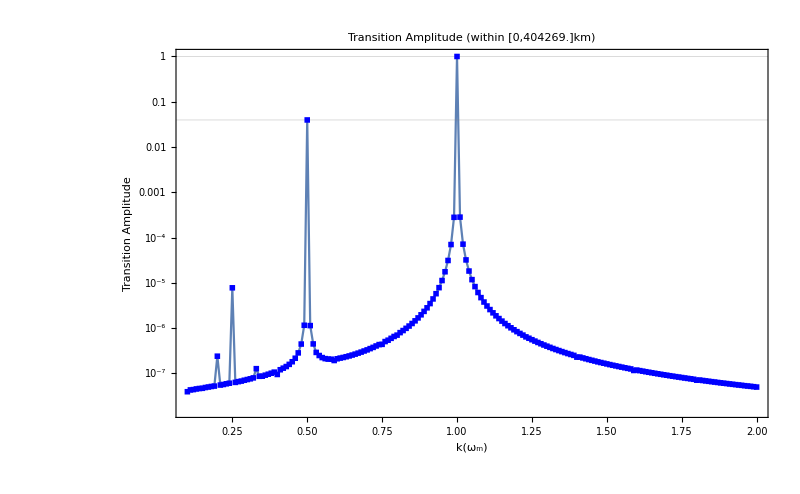

```mathematica
k1MaxAmpListDataListLogPlot=ListLogPlot[MapThread[{#1,#2}&,{k1MaxAmpListDatax,k1MaxAmpListData}],Joined->True,PlotMarkers->Style["■", Small, Blue],Frame->True,ImageSize->imgsize,PlotLabel->"Transition Amplitude (within [0,"<>ToString[Chop[MeVInverse2km[endpointNRes/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]]]]<>"]km)",FrameLabel->{{"Transition Amplitude",None},{"k(ω_m)","Fluction Wavelength (km)"}},FrameTicks->{{Automatic,None},{Automatic,k1MaxAmpListDataTicks}},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18},ImagePadding->{{Automatic,Automatic},{Automatic,60}},PlotRange->Full,GridLines->{None, {Max@probTransitListData[{0.5},oneaList,onephiList,thetamVRes,endpointNRes,10,0],Max@probTransitListData[{1},oneaList,onephiList,thetamVRes,endpointNRes,10,0]}}]
```

For Two frequencies

```mathematica
k2MaxAmpListDatak1=1;
k2MaxAmpListDatak2={0.1,1.1,0.01};
k2MaxAmpListDatax=Table[k2,{k2,k2MaxAmpListDatak2[[1]],k2MaxAmpListDatak2[[2]],k2MaxAmpListDatak2[[3]]}];
```

```mathematica
k2MaxAmpListData=Table[Max[probTransitListData[{k2MaxAmpListDatak1,k2},twoaList,twophiList,thetamVRes,endpointNRes,10,0]],{k2,k2MaxAmpListDatak2[[1]],k2MaxAmpListDatak2[[2]],k2MaxAmpListDatak2[[3]]}]
k2MaxAmpListDataFullTicks=Table[{k2,ScientificForm[MeVInverse2km[2Pi/(k2*OmegaMatter[thetamVRes,thetaVRes,omegaVRes])],2]},{k2,k2MaxAmpListDatak2[[1]],k2MaxAmpListDatak2[[2]],k2MaxAmpListDatak2[[3]]}];
k2MaxAmpListDataTicks=Take[k2MaxAmpListDataFullTicks,{1,Length@k2MaxAmpListDataFullTicks,Floor[(Length@k2MaxAmpListDataFullTicks)/5]}];
```

{0.998811,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998,0.999997,0.999994,0.999985,0.999935,0.999999,0.999929,0.999983,0.999993,0.999997,0.999999,0.999999,1.,1.,1.,1.}

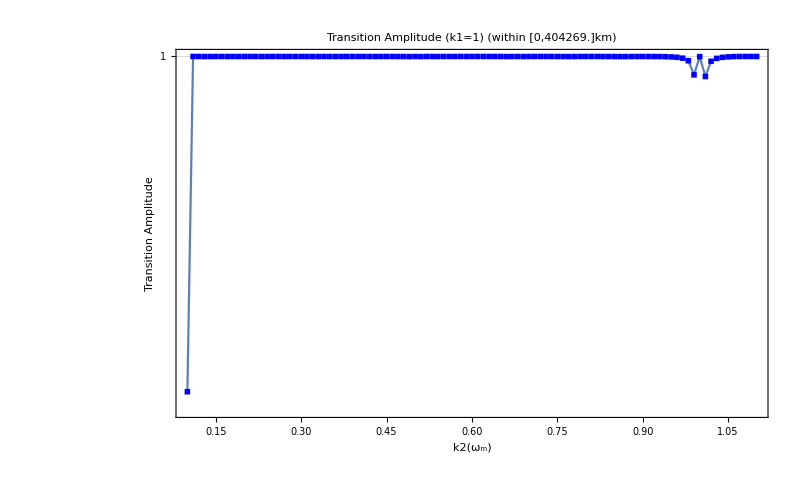

```mathematica
k2MaxAmpListDataListLogPlot=ListLogPlot[MapThread[{#1,#2}&,{k2MaxAmpListDatax,k2MaxAmpListData}],Joined->True,PlotMarkers->Style["■", Small, Blue],Frame->True,ImageSize->imgsize,PlotLabel->"Transition Amplitude (k1="<>ToString[k2MaxAmpListDatak1]<>") (within [0,"<>ToString[Chop[MeVInverse2km[endpointNRes/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]]]]<>"]km)",FrameLabel->{{"Transition Amplitude",None},{"k2(ω_m)","Fluction Wavelength (km)"}},FrameTicks->{{Automatic,None},{Automatic,k1MaxAmpListDataTicks}},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18},ImagePadding->{{Automatic,Automatic},{Automatic,60}},PlotRange->Full,GridLines->{None, {Max@probTransitListData[{k2MaxAmpListDatak1},oneaList,onephiList,thetamVRes,endpointNRes,10,0]}}]
```

Make Plots of some of the k’s

```mathematica
pltNum[{0.5},oneaList,onephiList,thetamVRes,endpointNRes*10,"Only 1",Blue,None,None]
```

-Graphics-

```mathematica
Manipulate[pltNum[{0.5,k2},{0.1,a2},twophiList,thetamVRes,endpointNRes*10,ToString[k2],Blue,None,None],{{k2,0.8},0.0001,1,0.0001},{{a2,0.1},0.001,0.2}]
```

```mathematica
Table[pltNum[{0.999,k2},{0.1,0.05},twophiList,thetamVRes,endpointNRes,"A1=A2=0.1; k1=0.999,"<>"k2="<>ToString[k2],Blue,None,None],{k2,0.9,1,0.1}]
```

{-Graphics-,-Graphics-}

```mathematica
Table[pltNum[{0.999,k2},twoaList,twophiList,thetamVRes,endpointNRes,ToString[k2],Blue,None,None],{k2,0.0001,1,0.2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}